```mathematica
B[x_, degree_]:=1/(Sqrt[2 * Pi])/;degree==0
```

```mathematica
B[ x_, degree_]:= Sin[Floor[(degree + 1) / 2] * x + Mod[degree , 2] * Pi/2]/Sqrt[Pi]/;degree!=0
```

```mathematica
B@@@Table[{x, i},{i, 0, 10}]
```

{1/(√(2 π)),Cos[x]/(√π),Sin[x]/(√π),Cos[2 x]/(√π),Sin[2 x]/(√π),Cos[3 x]/(√π),Sin[3 x]/(√π),Cos[4 x]/(√π),Sin[4 x]/(√π),Cos[5 x]/(√π),Sin[5 x]/(√π)}

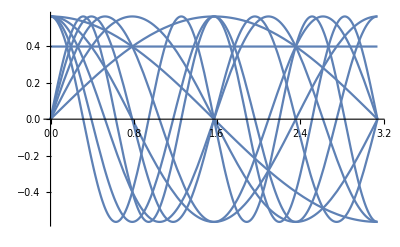

```mathematica
Plot[B@@@Table[{x, i},{i, 0, 10}], {x, 0, Pi}]
```

```mathematica
CoefA[degree_, l_][f_]:=(1/(2 *l))* Integrate[f[x], {x, -l, l}]/;degree == 0
CoefA[degree_, l_][f_] := (1/(l))* Integrate[f[x]* Cos[degree * x * Pi / l], {x, -l, l}]/;degree > 0
CoefB[degree_, l_][f_] :=(1/(l))* Integrate[f[x]* Sin[degree * x * Pi / l], {x, -l, l}]
```

```mathematica
ApproxFourier[degree_,  l_][f_] := CoefA[0, l][f] + Sum[CoefA[i, l][f] * Cos[i * x * Pi / l], {i, 1, degree}] + Sum[CoefB[i, l][f] * Sin[i * x * Pi / l], {i, 1 , degree}]
```

```mathematica
TestFunc[x_] := x
```

```mathematica
ApproxFourier[2, 5][TestFunc]./x=->y
```